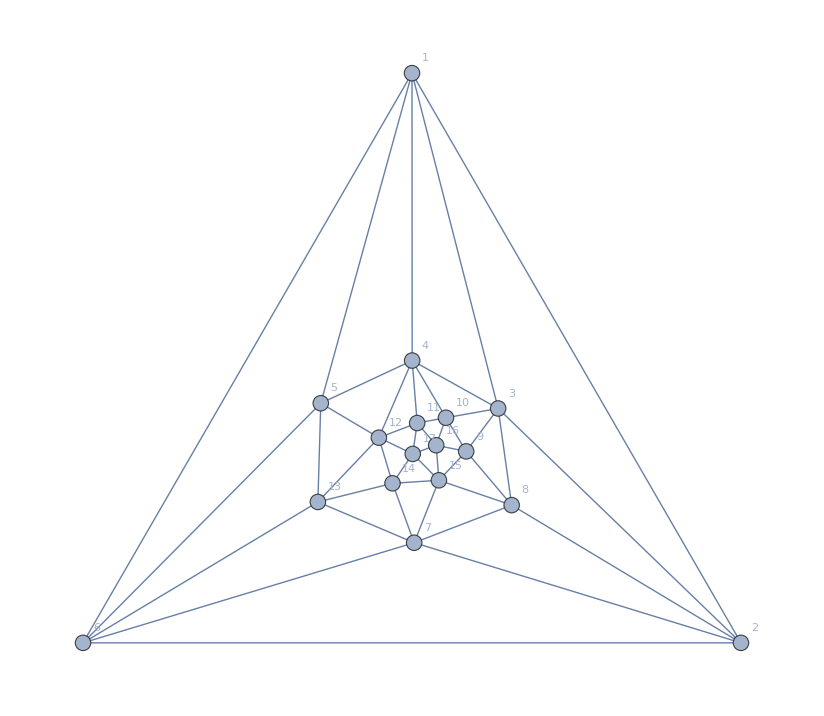

```mathematica
Graph[plantri[[8]],GraphLayout->"TutteEmbedding",VertexLabels->"Name"]
```

```mathematica
EmbedGraph5Plantri8[assoc_,key_]:=Block[{val=assoc[key], sets, reference={12,13,7,15,17}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[8]]],14];
g=EdgeDelete[ g,{7<->13,13<->12,12<->17,17<->15,15<->7}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
atomKeys
```

{29524,29525,29527,29533,29537,29551,29560,29605,29608,29633,29767,29768,29797,29857,29888,30253,30262,30334,30496,30586,31711,31714,31738,31954,31984,32441,32684,36085,36086,36112,36166,36194,36817,36898,38281,38308,39014,49207,49208,49210,49216,49220,49963,49972,51475,51478,52232,56011,56012,56770,58288,59048}

```mathematica
values=Monitor[
Table[
With[
{g=EmbedGraph5Plantri8[allGraphs,key]},
allGraphs[key,"colofour"]->{allGraphs[key,"graph"],ChromaticPolynomial[g,4]/24}
]
,{key,Sort[atomKeys]}
]
,
key]
```

{v1x2x3x4x5→{-Graphics-,0},v1x2x3x45→{-Graphics-,10},v1x2x35x4→{-Graphics-,6},v1x2x34x5→{-Graphics-,20},v1x2x345→{-Graphics-,14},v1x25x3x4→{-Graphics-,11},v1x25x34→{-Graphics-,31},v1x24x3x5→{-Graphics-,6},v1x24x35→{-Graphics-,0},v1x245x3→{-Graphics-,10},v1x23x4x5→{-Graphics-,10},v1x23x45→{-Graphics-,14},v1x235x4→{-Graphics-,10},v1x234x5→{-Graphics-,14},v1x2345→{-Graphics-,11},v15x2x3x4→{-Graphics-,11},v15x2x34→{-Graphics-,29},v15x24x3→{-Graphics-,8},v15x23x4→{-Graphics-,16},v15x234→{-Graphics-,11},v14x2x3x5→{-Graphics-,9},v14x2x35→{-Graphics-,3},v14x25x3→{-Graphics-,8},v14x23x5→{-Graphics-,8},v14x235→{-Graphics-,4},v145x2x3→{-Graphics-,20},v145x23→{-Graphics-,12},v13x2x4x5→{-Graphics-,9},v13x2x45→{-Graphics-,8},v13x25x4→{-Graphics-,8},v13x24x5→{-Graphics-,3},v13x245→{-Graphics-,4},v135x2x4→{-Graphics-,13},v135x24→{-Graphics-,5},v134x2x5→{-Graphics-,7},v134x25→{-Graphics-,9},v1345x2→{-Graphics-,16},v12x3x4x5→{-Graphics-,11},v12x3x45→{-Graphics-,16},v12x35x4→{-Graphics-,8},v12x34x5→{-Graphics-,29},v12x345→{-Graphics-,11},v125x3x4→{-Graphics-,21},v125x34→{-Graphics-,26},v124x3x5→{-Graphics-,13},v124x35→{-Graphics-,5},v1245x3→{-Graphics-,18},v123x4x5→{-Graphics-,20},v123x45→{-Graphics-,12},v1235x4→{-Graphics-,18},v1234x5→{-Graphics-,16},v12345→{-Graphics-,16}}

## Here we have the results

To my surprise we see that only one triangle has a zero embedded colofour.

```mathematica
TableForm[Sort[values,#1[[2,2]]<#2[[2,2]]&]]
```

v1x24x35→{-Graphics-,0}
v1x2x3x4x5→{-Graphics-,0}
v13x24x5→{-Graphics-,3}
v14x2x35→{-Graphics-,3}
v13x245→{-Graphics-,4}
v14x235→{-Graphics-,4}
v124x35→{-Graphics-,5}
v135x24→{-Graphics-,5}
v1x24x3x5→{-Graphics-,6}
v1x2x35x4→{-Graphics-,6}
v134x2x5→{-Graphics-,7}
v12x35x4→{-Graphics-,8}
v13x25x4→{-Graphics-,8}
v13x2x45→{-Graphics-,8}
v14x23x5→{-Graphics-,8}
v14x25x3→{-Graphics-,8}
v15x24x3→{-Graphics-,8}
v134x25→{-Graphics-,9}
v13x2x4x5→{-Graphics-,9}
v14x2x3x5→{-Graphics-,9}
v1x235x4→{-Graphics-,10}
v1x23x4x5→{-Graphics-,10}
v1x245x3→{-Graphics-,10}
v1x2x3x45→{-Graphics-,10}
v12x345→{-Graphics-,11}
v12x3x4x5→{-Graphics-,11}
v15x234→{-Graphics-,11}
v15x2x3x4→{-Graphics-,11}
v1x2345→{-Graphics-,11}
v1x25x3x4→{-Graphics-,11}
v123x45→{-Graphics-,12}
v145x23→{-Graphics-,12}
v124x3x5→{-Graphics-,13}
v135x2x4→{-Graphics-,13}
v1x234x5→{-Graphics-,14}
v1x23x45→{-Graphics-,14}
v1x2x345→{-Graphics-,14}
v12345→{-Graphics-,16}
v1234x5→{-Graphics-,16}
v12x3x45→{-Graphics-,16}
v1345x2→{-Graphics-,16}
v15x23x4→{-Graphics-,16}
v1235x4→{-Graphics-,18}
v1245x3→{-Graphics-,18}
v123x4x5→{-Graphics-,20}
v145x2x3→{-Graphics-,20}
v1x2x34x5→{-Graphics-,20}
v125x3x4→{-Graphics-,21}
v125x34→{-Graphics-,26}
v12x34x5→{-Graphics-,29}
v15x2x34→{-Graphics-,29}
v1x25x34→{-Graphics-,31}

## Verify the result

```mathematica
amigo1Key=First[Select[Keys[allGraphs],With[{g=allGraphs[#,"graph"]},
VertexCount[g]==5&&EdgeCount[g]==7&&
EdgeQ[g,1<->2]&&
EdgeQ[g,2<->3]&&
EdgeQ[g,3<->4]&&
EdgeQ[g,4<->5]&&
EdgeQ[g,5<->1]&&
EdgeQ[g,1<->3]&&
EdgeQ[g,1<->4]
]&]]
```

29413

```mathematica
amigo2Key=First[Select[Keys[allGraphs],With[{g=allGraphs[#,"graph"]},
VertexCount[g]==5&&EdgeCount[g]==7&&
EdgeQ[g,1<->2]&&
EdgeQ[g,2<->3]&&
EdgeQ[g,3<->4]&&
EdgeQ[g,4<->5]&&
EdgeQ[g,5<->1]&&
EdgeQ[g,2<->5]&&
EdgeQ[g,2<->4]
]&]]
```

20773

```mathematica
amigo3Key=First[Select[Keys[allGraphs],With[{g=allGraphs[#,"graph"]},
VertexCount[g]==5&&EdgeCount[g]==7&&
EdgeQ[g,1<->2]&&
EdgeQ[g,2<->3]&&
EdgeQ[g,3<->4]&&
EdgeQ[g,4<->5]&&
EdgeQ[g,5<->1]&&
EdgeQ[g,3<->5]&&
EdgeQ[g,3<->1]
]&]]
```

27229

```mathematica
amigo4Key=First[Select[Keys[allGraphs],With[{g=allGraphs[#,"graph"]},
VertexCount[g]==5&&EdgeCount[g]==7&&
EdgeQ[g,1<->2]&&
EdgeQ[g,2<->3]&&
EdgeQ[g,3<->4]&&
EdgeQ[g,4<->5]&&
EdgeQ[g,5<->1]&&
EdgeQ[g,4<->1]&&
EdgeQ[g,4<->2]
]&]]
```

22933

```mathematica
amigo5Key=First[Select[Keys[allGraphs],With[{g=allGraphs[#,"graph"]},
VertexCount[g]==5&&EdgeCount[g]==7&&
EdgeQ[g,1<->2]&&
EdgeQ[g,2<->3]&&
EdgeQ[g,3<->4]&&
EdgeQ[g,4<->5]&&
EdgeQ[g,5<->1]&&
EdgeQ[g,5<->3]&&
EdgeQ[g,5<->2]
]&]]
```

20695

```mathematica
ChromaticPolynomial[EmbedGraph5Plantri8[allGraphs,29413],4]/24
```

23

```mathematica
allGraphs[29413,"colofour"]/.values
```

{-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-,23}

```mathematica
ChromaticPolynomial[EmbedGraph5Plantri8[allGraphs,20773],4]/24
```

27

```mathematica
allGraphs[20773,"colofour"]/.values
```

{-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-,27}

## Trying to find a link between the alfa beta an dthe quadrilaterals

```mathematica
valuesalfa=Monitor[
Table[
With[
{g=EmbedGraph5Plantri8[allGraphs,key]},
allGraphs[key,"colofour"]->{allGraphs[key,"graph"],ChromaticPolynomial[g,4]/24}
]
,{key,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}
]
,
key]
```

{v13x24x5→{-Graphics-,3},v14x25x3→{-Graphics-,8},v1x24x35→{-Graphics-,0},v13x25x4→{-Graphics-,8},v14x2x35→{-Graphics-,3}}

```mathematica
Total[Map[#[[2,2]]&,valuesalfa]]
```

22

```mathematica
valuesquad=Monitor[
Table[
With[
{g=EmbedGraph5Plantri8[allGraphs,key]},
allGraphs[key,"colofour"]->{allGraphs[key,"graph"],ChromaticPolynomial[g,4]/24}
]
,{key,{29605,36085,29551,31711,29527}}
]
,
key]
```

{v1x24x3x5→{-Graphics-,6},v13x2x4x5→{-Graphics-,9},v1x25x3x4→{-Graphics-,11},v14x2x3x5→{-Graphics-,9},v1x2x35x4→{-Graphics-,6}}

```mathematica
Total[Map[#[[2,2]]&,valuesquad]]
```

41

```mathematica
IsomorphicGraphQ[DualGraph[Faces[GraphData["PetersenGraph"]]],CompleteGraph[7]]
```

True

```mathematica
GraphData["PetersenGraph","CochromaticGraphs"]
```

{}

```mathematica
GraphData["PetersenGraph","FlowPolynomial"][x]
```

(-4+x) (-3+x) (-2+x) (-1+x) (10-5 x+x^2)

```mathematica
GraphData["PetersenGraph","ChromaticPolynomial"][x]
```

(-2+x) (-1+x) x (-352+775 x-814 x^2+529 x^3-230 x^4+67 x^5-12 x^6+x^7)

```mathematica
GraphData["PetersenGraph","FlowPolynomial"][x]
```

(-4+x) (-3+x) (-2+x) (-1+x) (10-5 x+x^2)

```mathematica
FlowPolynomial[CompleteGraph[7],x]//Factor
```

(-1+x) (7575-34365 x+81625 x^2-133100 x^3+163756 x^4-158405 x^5+122785 x^6-76785 x^7+38655 x^8-15497 x^9+4845 x^10-1140 x^11+190 x^12-20 x^13+x^14)

```mathematica
FlowPolynomial[DualGraph[Faces[CompleteGraph[4]]],x]//Factor
```

(-3+x) (-2+x) (-1+x)

```mathematica
ChromaticPolynomial[CompleteGraph[4],x]//Factor
```

(-3+x) (-2+x) (-1+x) x

```mathematica
FlowPolynomial[DualGraph[Faces[allGraphs[29413,"graph"]]]][x]//Factor
```

(-2+x) (-1+x)

```mathematica
ChromaticPolynomial[allGraphs[29413,"graph"],x]//Factor
```

(-2+x)^3 (-1+x) x

```mathematica
allGraphs[29413,"graph"]
```

-Graphics-

```mathematica
Faces[allGraphs[29413,"graph"]]
```

{{1<->2,1<->3,2<->3},{1<->3,1<->4,3<->4},{1<->4,1<->5,4<->5}}

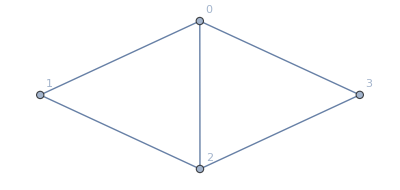

```mathematica
Graph[DualGraph[Faces[allGraphs[29413,"graph"]]],VertexLabels->"Name"]
```

```mathematica
Reduce[x-a>b,x]
```

(a|b)∈Reals&&x>a+b